Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# Práctica 2 (17 septiembre de 2024) Números reales

Inecuaciones, desigualdades, conjuntos acotados, cotas, ínfimo, supremo.

Cuestiones previas.

	Reduce Con la instrucción Reduce podemos resolver (o simplificar)  ecuaciones e inecuaciones. Como es habitual, la inicial se escribe en mayúscula, y el resto en minúsculas. Tras el corchete escribimos la ecuación (con doble igual ==) o inecuación (con <, <=, >, >=, o utilizando la paleta).
	
	Plot En muchos casos, con la instrucción Plot podríamos también tener una idea de la solución de la ecuación o inecuación (aunque podría también inducirnos a error, pues sólo vemos un trozo de las gráficas).

## Ejercicios (del tema de números reales)

## 2) Representar en la recta real los valores de x que cumplen las expresiones siguientes. Expresarlos, si es posible, como un intervalo o unión de varios intervalos. Decir si están acotados, superior o inferiormente, y, en ese caso, calcular el supremo y/o el ínfimo: a) 3 x - 2 < x + 5 c) 6/(x - 1)⩾ 10 l) |x| ⩽ 3

```mathematica
Reduce[3x-2<x+5,x]
```

x<7/2

La respuesta que nos da es que x debe ser menor que 7/2. 
El conjunto de soluciones es por tanto el intervalo (-∞,7/2). Está acotado superiormente, pero no inferiormente. Cualquier número mayor o igual que 7/2 es una cota superior. El 7/2 es el supremo del conjunto, que en este caso no pertenece al conjunto. El conjunto no tiene cotas inferiores, por ello no tiene ínfimo (que es la mayor de las cotas inferiores).

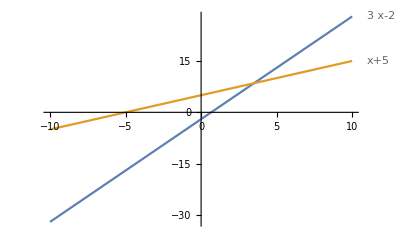

```mathematica
Plot[{3x-2,x+5},{x,-10,10},PlotLabels->"Expressions"]
```

Con la instrucción Plot, hemos dibujado las dos partes de la desigualdad y las hemos etiquetado. Vemos que x+5 (color naranja) está por encima de 3x-2 (color azul) antes de un valor de x entre 3 y 4. Para precisar más podríamos reducir el intervalo donde se dibujan las gráficas.

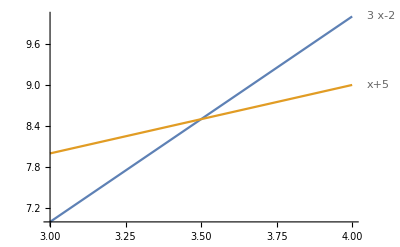

```mathematica
Plot[{3x-2,x+5},{x,3,4},PlotLabels->"Expressions"]
```

```mathematica
Reduce[6/(x-1)≥ 10,x]
```

1<x≤8/5

La respuesta que nos da es que x debe ser mayor que 1 y menor o igual que 8/5.
El conjunto de soluciones es el intervalo (1,8/5]. Está acotado superior e inferiormente. Podemos decir simplemente que está acotado.Cualquier número mayor o igual que 8/5 es una cota superior. El 8/5 es el supremo del conjunto, que en este caso sí pertenece al conjunto. Cualquier número menor o igual a 1 es una cota inferior. El 1 es el ínfimo (la mayor de las cotas inferiores), en este caso no pertenece al conjunto.

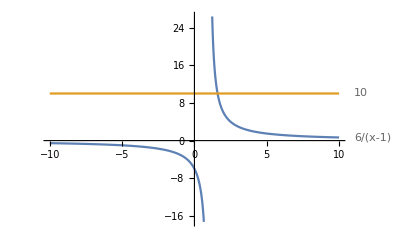

```mathematica
Plot[{6/(x-1),10},{x,-10,10},PlotLabels->"Expressions"]
```

```mathematica
Reduce[Abs[x]≤3,x]
```

x==-3||(-3<Re[x]<3&&-√(9-Re[x]^2)≤Im[x]≤√(9-Re[x]^2))||x==3

El valor absoluto, |x|, es una función que para el Mathematica se extiende a los números complejos como la función módulo. Por ello nos da como solución de la inecuación |x| ⩽ 3 valores complejos. Para evitar esto podemos precisar que trabajamos con números reales.

```mathematica
Reduce[Abs[x]≤3,x,Reals]
```

-3≤x≤3

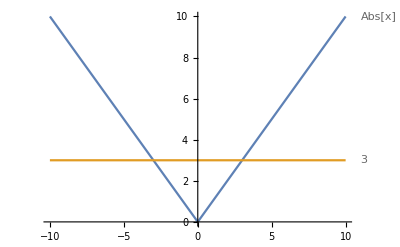

```mathematica
Plot[{Abs[x],3},{x,-10,10},PlotLabels->"Expressions"]
```

La respuesta que nos da es que x debe ser mayor o igual que -3 y menor o igual que 3.
El conjunto de soluciones es el intervalo [-3,3]. Está acotado superior e inferiormente. Podemos decir simplemente que está acotado.Cualquier número mayor o igual que 3 es una cota superior. El 3 es el supremo del conjunto, que en este caso sí pertenece al conjunto. Cualquier número menor o igual que -3 es una cota inferior. El -3 es el ínfimo (la mayor de las cotas inferiores), en este caso también pertenece al conjunto.

## 3) Resolver la ecuación: |1+|2-x||=3

```mathematica
Reduce[Abs[1+Abs [2-x]]==3,x,Reals]
```

x==0||x==4

En este caso es una ecuación y tiene dos soluciones, 0 y 4.

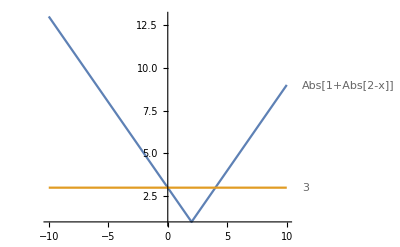

```mathematica
Plot[{Abs[1+Abs [2-x]],3},{x,-10,10},PlotLabels->"Expressions"]
```

Las soluciones son los valores de x donde se producen los cortes entre las dos gráficas, el 0 y el 4.

## 4) Representar en la recta real los valores de x que cumplen las expresiones siguientes. Expresarlos, si es posible, como un intervalo o unión de varios intervalos. Decir si están acotados, superior o inferiormente, y, en ese caso, calcular el supremo y/o el ínfimo: d) |3x - 5| ⩾ 7 e) |5 - 2/x| < 1

```mathematica
Reduce[Abs[3x-5]≥7,x,Reals]
```

x≤-2/3||x≥4

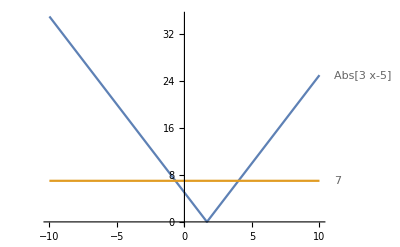

```mathematica
Plot[{Abs[3x-5],7},{x,-10,10},PlotLabels->"Expressions"]
```

Los valores que cumplen la condición |3x - 5|  ⩾ 7, son los números reales menores o iguales que -2/3 o mayores o iguales que 4. Se trata de un conjunto que no está acotado (ni superior, ni inferiormente). Escribiríamos el conjunto como la unión de dos intervalos, (-∞,-2/3] ∪ [4, ∞). Es un conjunto que no está acotado ni inferior, ni superiormente. No tiene supremo, ni ínfimo.

```mathematica
Reduce[Abs[5-2/x]<1,x,Reals]
```

1/3<x<1/2

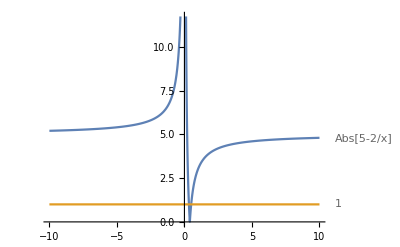

```mathematica
Plot[{Abs[5-2/x],1},{x,-10,10},PlotLabels->"Expressions"]
```

Los valores que cumplen la condición Abs[5-2/x]<1, son los números reales mayores que 1/3 y menores que 1/2.  Escribiríamos el intervalo (1/3,1/2).
Se trata de un conjunto acotado superiormente (el 1, o el 2, o el número Pi son cotas superiores). También es un conjunto acotado inferiormente (-3, 0 ó 0.1 son ejemplos de cotas inferiores).
El supremo, la menor de las cotas superiores, es el 1/2. El ínfimo, la mayor de las cotas inferiores, es 1/3. En este caso, ni el supremo ni el ínfimo están dentro del conjunto.